# Q7

It is straight line

52.125

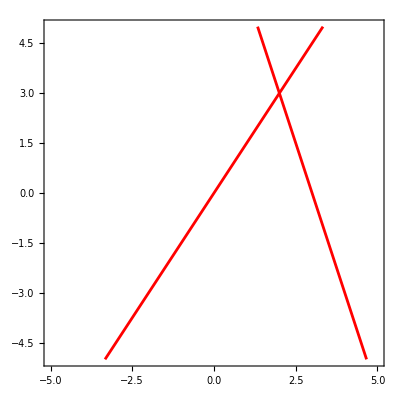

It is straight line

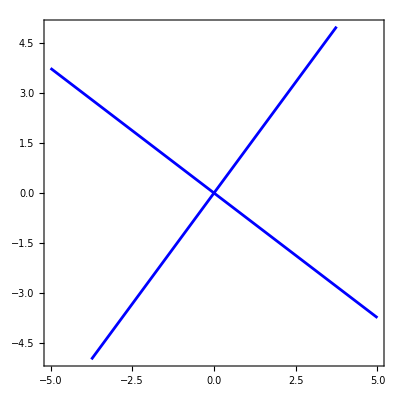

It is straight line

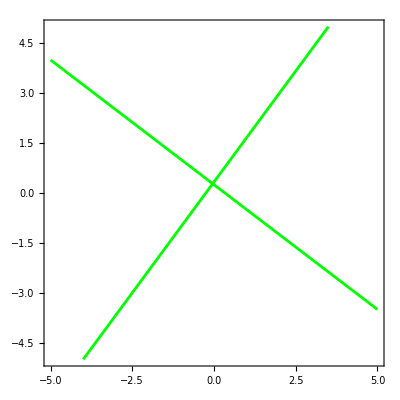

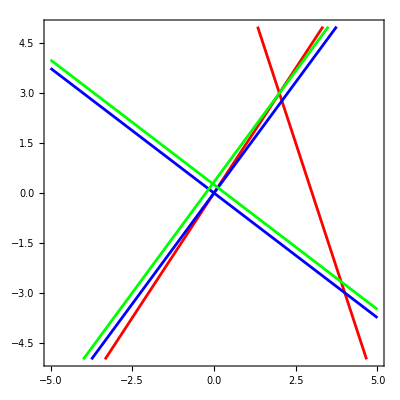

{{λ→4}}

```mathematica
f1[x_,y_]:=9 x^2-3x*y-2 y^2-27x+18y(*i*)
f2[x_,y_]:=12 x^2+7x*y-12 y^2(*ii*)
f3[x_,y_]:=12 x^2+7x*y-12 y^2-x+7y-1(*iii*)
(*a*)
If[
Det[({{9, -3/2, -27/2}, {-3/2, -2, 9}, {-27/2, 9, 0}})]==0,
Print["It is straight line"],
Print["It is not straight line"]
]
Reduce[f1[x,y]==0,{x,y}];
f4[x_,y_]:=3x+y-9
f5[x_,y_]:=3x-2y
s=Solve[f4[x,y]==0&&f5[x,y]==0,{x,y}];
θ=ArcTan[Abs[(-3-1.5)/(1+(-3)*1.5)]]*180/Pi//N
g1= ContourPlot[
{y==9-3 x,y==(3 x)/2},
{x,-5,5},
{y,-5,5},
ContourStyle->Red
]
(*b*)
If[
Det[({{12, 7/2, 0}, {7/2, -12, 0}, {0, 0, 0}})]==0,
Print["It is straight line"],
Print["It is not straight line"]
]
Reduce[f2[x,y]==0,{x,y}];
g2= ContourPlot[{y==-(3 x)/4,y==(4 x)/3},{x,-5,5},{y,-5,5},ContourStyle->Blue]
If[
Det[({{12, 7/2, -1/2}, {7/2, -12, 7/2}, {-1/2, 7/2, -1}})]==0,
Print["It is straight line"],
Print["It is not straight line"]
]
Reduce[f3[x,y]==0,{x,y}];
g3= ContourPlot[{y==1/4-(3 x)/4,y==1/3+(4 x)/3},{x,-5,5},{y,-5,5},ContourStyle->Green]
Show[g1,g2,g3]
(*c*)
Solve[Det[({{λ, 2, -2}, {2, 1, -1}, {-2, -1, -3}})]==0,λ]
```